### First, generate a discritized normal distribution & plot it fastest change is at σ

```mathematica
Clear[x]
D[1/(√(2π) σ)ⅇ^(-1/(2 σ^2)(x^2)),x]
```

```mathematica
Maximize[-(ⅇ^(-x^2/(2 σ^2)) x)/(√(2 π) σ^3),x]
```

```mathematica
Maximize[-(ⅇ^(-x^2/(2  5)) x)/(√(2 π)),x]
```

{√(5/(2 ⅇ π)),{x→-√5}}

```mathematica
normal2[x_,y_,σ_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2+y^2))
normal1[x_,σ_]:=1/(√(2π) σ)ⅇ^(-1/(2 σ^2)(x^2))
genNormal1dHist[n_,σ_,w_]:=Module[{ds},(*make a n grid with variance σ and range -w/2 to w/2, normalizes this*)
ds = Table[ 1/(√(2π) σ)ⅇ^(-1/(2 σ^2)(x^2)),{x,-w/2,w/2,w/(n-1)}];
ds = ds/Total[ds,2]]
genNormal2dHist[n_,σ_,w_]:=Module[{ds},(*make a n×n grid with variance σ and range -w/2 to w/2, normalizes this*)
ds = Table[ 1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2+y^2)),{x,-w/2,w/2,w/n},{y,-w/2,w/2,w/n}];
ds = ds/Total[ds,2]]
```

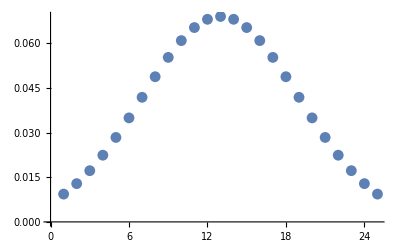
{0.01129,-Graphics-}

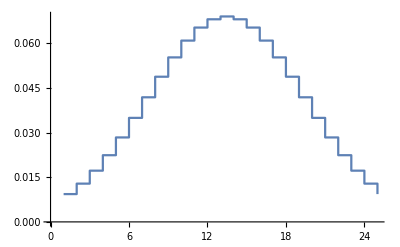
{0.01337,-Graphics-}

```mathematica
Timing[ListPlot[genNormal1dHist[25,1,4]]]
Timing[ListPlot[genNormal1dHist[25,1,4],PlotRange->All,Mesh->None,Joined->True,(*Filling->Bottom,*)InterpolationOrder->0]]
```

```mathematica
Timing[ListPlot3D[genNormal2dHist[25,1,4]]]
```

{0.07794,-Graphics3D-}

```mathematica
Timing[ListPlot3D[genNormal2dHist[25,1,4],PlotRange->All,Mesh->None,(*Filling->Bottom,*)InterpolationOrder->0]]
```

{0.06785,-Graphics3D-}

```mathematica
Timing[ListPlot3D[genNormal2dHist[25,1,4],PlotRange->All,Mesh->None,Filling->Bottom,InterpolationOrder->0]]
```

{0.09909,-Graphics3D-}

```mathematica
Timing[ListPlot3D[genNormal2dHist[10,1,4],PlotRange->All,Mesh->None,Filling->Bottom,InterpolationOrder->0]]
```

{0.01948,-Graphics3D-}

### next, generate a plausible transition function starting from the center.

```mathematica
m=genNormal2dHist[3,1,4];
N[m]//MatrixForm
```

(0.0113437 | 0.0838195 | 0.0113437
0.0838195 | 0.619347 | 0.0838195
0.0113437 | 0.0838195 | 0.0113437)

#### Assume k percent leaves the center, then

```mathematica
p = ConstantArray[0,{9,9}];
MatrixForm[p]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
n = 3;
m=genNormal1dHist[n,1,4];
N[m]//MatrixForm
p = DiagonalMatrix[ConstantArray[1,n]];
MatrixForm[p]
```

(0.106507
0.786986
0.106507)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
k = .1;
p = DiagonalMatrix[ConstantArray[1,n]];
For[ i=Ceiling[n/2],i>0,i--, 
If[i==Ceiling[n/2],
p⟦i,i⟧ = p⟦i,i⟧ -2k;
p⟦i,i-1⟧= k;
p⟦i,i+1⟧= k;];
If[i==1,
p⟦1,2⟧=p⟦2,1⟧*m⟦2⟧/m⟦1⟧;
p⟦1,1⟧= 1-p⟦1,2⟧;
p⟦n,n-1⟧=p⟦1,2⟧;
p⟦n,n⟧=p⟦1,1⟧;
];
If[i<Ceiling[n/2]&&i>1,
p⟦i,i+1⟧=p⟦i+1,i⟧*m⟦i+1⟧/m⟦i⟧;
p⟦i,i-1⟧=k-p⟦i,i+1⟧;
p⟦i,i⟧= 1-p⟦i,i+1⟧-p⟦i,i-1⟧;

p⟦n,n-1⟧=p⟦i,i+1⟧;
p⟦n,n+1⟧=p⟦i,i-1⟧;
p⟦n,n⟧=p⟦i,i⟧;

];
];
```

```mathematica
MatrixForm[N[m]]
MatrixForm[p.p.m]
```

(0.106507
0.786986
0.106507)

(0.640036
0.642576
0.640036)